```mathematica
string=NotebookDirectory[];
FileTensorAnalysis=string<>"TensorAnalysis.nb";
FileFuncao1=string<>"Funcao1.nb";
FileFuncao2=string<>"Funcao2.nb";
vecStrings={FileTensorAnalysis,FileFuncao1,FileFuncao2};
For[is=1,is≤Length[vecStrings],is++,
nb=NotebookOpen[vecStrings[[is]]];
SelectionMove[nb,All,Notebook];
SelectionEvaluate[nb];
NotebookClose[nb];
]
```

```mathematica
Function1[Log[A/C]/B/.exemple,0]
LFunction[EpsEqL[Log[A/C]/B/.exemple]]
```

-2.77556×10^-17

0.489305

```mathematica
ElastoPlasticL[L_,EP_,ETotal_]:=Block[{Lnext,θnext,EPnext,valf1,valf2,SigI1xJ2,SigTrial,EElast,EElastIJ,delL,I1next,J2next,lval,diffsig,diffsigIJ,sigresult,IJQuadrant,epsp,epsprev,epsmax,pr},
pr=True;
Lnext=L;
EElast=ETotal-EP;
EElastIJ=ToIJ[EElast];
IJQuadrant=EElastIJ[[3]];
SigI1xJ2={3 K EElastIJ[[1]],2G EElastIJ[[2]],IJQuadrant}/.exemple;
SigTrial=FromIJ[SigI1xJ2];
valf1=Function1[SigI1xJ2[[1]],SigI1xJ2[[2]]] // Chop;
valf2=Function2L[SigI1xJ2[[1]],SigI1xJ2[[2]],L]//Chop;
epsmax=2;
If[pr,
Print["ETotal = ",ETotal];
Print["SigI1xJ2 = ",SigI1xJ2];
Print["L ",L];
Print["valf1 = ",valf1];
Print["valf2 = ",valf2];
];
If[(valf2≤ 0 && SigI1xJ2[[1]] ≤  L) || (valf1 ≤ 0 && SigI1xJ2[[1]] ≥ L),
Print["Elastic"];
Lnext = L;
sigresult=FromIJ[SigI1xJ2];
EPnext=EP
,If[valf2 >0 && SigI1xJ2[[1]] ≤ L,
Print["Project F2"];
{θnext,delL}=NewtonFuncL[L,SigI1xJ2];
Lnext=L+delL;
lval=Lnext;
I1next=lval+F[lval]R Cos[θnext]/.exemple;
J2next=F[lval]Sin[θnext]/.exemple;
Print["Function2L = ",Function2L[I1next,J2next,Lnext]];
sigresult=FromIJ[{I1next,J2next,IJQuadrant}];
diffsig=FromIJ[SigI1xJ2]-FromIJ[{I1next,J2next,IJQuadrant}];
diffsigIJ=ToIJ[diffsig];
EPnext=EP+FromIJ[{diffsigIJ[[1]]/(3 K),diffsigIJ[[2]]/(2G),diffsigIJ[[3]]}]/.exemple;
,
Print["Project F1"];
I1next=NewtonF1[SigI1xJ2];
J2next = F[I1next]/.exemple;
If[J2next<0,
Print["Point is wasted J2next = ",J2next];
I1next=Log[A/C]/B/.exemple;
J2next = 0.;
epsmax=EpsEqL[I1next]/.exemple;
Print[" eps max ",epsmax];
];
Print["Function 1 I1next ",I1next," J2next ",J2next," value ",Function1[I1next,J2next]];
sigresult=FromIJ[{I1next,J2next,IJQuadrant}];
diffsig=FromIJ[SigI1xJ2]-sigresult;
diffsigIJ=ToIJ[diffsig];
EPnext=EP+FromIJ[{diffsigIJ[[1]]/(3K),diffsigIJ[[2]]/(2G),diffsigIJ[[3]]}]/.exemple;
epsprev = EpsEqL[L]/.exemple;
epsp=epsprev+diffsigIJ[[1]]/(3K)/.exemple;
If[epsp > epsmax,epsp=epsmax];
Lnext=LFunction[epsp]/.exemple;
Print["epsprev ",epsprev, " epspnext ",epsp," Lprev ",L," Lnext ",Lnext]; 
If[I1next<Lnext,Print["******* Should have projected onto F2 ***********"]];.08 
]
];
{Lnext,EPnext,sigresult,SigTrial}
]
locL=LFunction[0]
EP={0,0};

ETotal={0.05/3,0.0};
ElastoPlasticL[0,EP,ETotal]

ETotal={-0.065/50,0.0};
ElastoPlasticL[locL,EP,ETotal]
```

0.133045

ETotal = {0.0166667,0.}

SigI1xJ2 = {3.33333,192.45,-1}

L 0

valf1 = 193.88

valf2 = 7.55894×10^6

Project F1

sigtrial {3.33333,192.45,-1}

I1 start value 0.9

I1Val = 0.858002

F[I1] = -0.0698391

Diffval = 2.22045×10^-16

Point is wasted J2next = -0.0698391

eps max 0.0256667

Function 1 I1next 0.490305 J2next 0. value -2.77556×10^-17

epsprev -0.00730205 epspnext 0.00691309 Lprev 0 Lnext 0.24382

{0.24382,{0.0158495,-0.000817174},{0.163435,0.163435},{223.333,-110.}}

ETotal = {-0.0013,0.}

SigI1xJ2 = {-0.26,15.0111,1}

L 0.133045

valf1 = 14.9123

valf2 = 79570.4

Project F2

residue = {-0.0251659,0.00786118}

residue = {-0.00800615,-1.5986×10^-6}

residue = {-0.00214037,1.51022×10^-7}

residue = {-0.00057218,1.15336×10^-8}

residue = {-0.000152945,8.39508×10^-10}

residue = {-0.0000408816,6.02758×10^-11}

residue = {-0.0000109274,4.31294×10^-12}

Function2L = -4.47132×10^-17

{0.101816,{-0.00146543,-0.000170389},{-0.0324082,0.0668245},{-17.42,8.58}}

```mathematica
ListETotalL=Table[{epsa,0},{epsa,0,-0.06,-0.06/12}]
AppendTo[ListETotalL,Table[{epsa,0},{epsa,-0.06,-0.046,0.002}]]
AppendTo[ListETotalL,Table[{epsa,0},{epsa,-0.046,0.014,0.01}]]
(*ListETotalL=Join[ListETotalL,Reverse[ListETotalL]]*)
ResultL={{LFunction[0],{0,0},{0,0},{0,0}}};
test=ElastoPlasticL[ResultL[[-1,1]],ResultL[[-1,2]],ListETotalL[[2]]]
ElastoPlasticL[test[[1]],test[[2]],ListETotalL[[2]]]

For[i=2,i<=Length[ListETotalL],i++,
AppendTo[ResultL,ElastoPlasticL[ResultL[[-1,1]],ResultL[[-1,2]],ListETotalL[[i]]]]
]
ElastoPlasticL[ResultL[[-1,1]],ResultL[[-1,2]],ListETotalL[[-1]]]
```

{{0.,0},{-0.005,0},{-0.01,0},{-0.015,0},{-0.02,0},{-0.025,0},{-0.03,0},{-0.035,0},{-0.04,0},{-0.045,0},{-0.05,0},{-0.055,0},{-0.06,0}}

{{0.,0},{-0.005,0},{-0.01,0},{-0.015,0},{-0.02,0},{-0.025,0},{-0.03,0},{-0.035,0},{-0.04,0},{-0.045,0},{-0.05,0},{-0.055,0},{-0.06,0},{{-0.06,0},{-0.058,0},{-0.056,0},{-0.054,0},{-0.052,0},{-0.05,0},{-0.048,0},{-0.046,0}}}

{{0.,0},{-0.005,0},{-0.01,0},{-0.015,0},{-0.02,0},{-0.025,0},{-0.03,0},{-0.035,0},{-0.04,0},{-0.045,0},{-0.05,0},{-0.055,0},{-0.06,0},{{-0.06,0},{-0.058,0},{-0.056,0},{-0.054,0},{-0.052,0},{-0.05,0},{-0.048,0},{-0.046,0}},{{-0.046,0},{-0.036,0},{-0.026,0},{-0.016,0},{-0.006,0},{0.004,0},{0.014,0}}}

ETotal = {-0.005,0}

SigI1xJ2 = {-1.,57.735,1}

L 0.133045

valf1 = 57.5771

valf2 = 1.17703×10^6

Project F2

residue = {-0.048155,0.0534208}

residue = {-0.00755245,0.0000343401}

residue = {-0.000732123,2.32866×10^-7}

residue = {-0.000070777,2.43885×10^-9}

residue = {-6.84093×10^-6,2.29965×10^-11}

residue = {-6.61194×10^-7,2.16271×10^-13}

residue = {-6.39061×10^-8,6.66134×10^-16}

Function2L = 1.28215×10^-16

{0.0402457,{-0.0050625,-0.00006814},{-0.0618957,0.0508262},{-67.,33.}}

ETotal = {-0.005,0}

SigI1xJ2 = {0.0397568,0.06508,1}

L 0.0402457

valf1 = -0.0000608553

valf2 = 0

Elastic

{0.0402457,{-0.0050625,-0.00006814},{-0.0618957,0.0508262},{-0.0618957,0.0508262}}

ETotal = {-0.005,0}

SigI1xJ2 = {-1.,57.735,1}

L 0.133045

valf1 = 57.5771

valf2 = 1.17703×10^6

Project F2

residue = {-0.048155,0.0534208}

residue = {-0.00755245,0.0000343401}

residue = {-0.000732123,2.32866×10^-7}

residue = {-0.000070777,2.43885×10^-9}

residue = {-6.84093×10^-6,2.29965×10^-11}

residue = {-6.61194×10^-7,2.16271×10^-13}

residue = {-6.39061×10^-8,6.66134×10^-16}

Function2L = 1.28215×10^-16

ETotal = {-0.01,0}

SigI1xJ2 = {-0.960243,57.8001,1}

L 0.0402457

valf1 = 57.6447

valf2 = 788820.

Project F2

residue = {-0.0420519,0.0448331}

residue = {-0.00723976,0.0000234805}

residue = {-0.000797568,2.61443×10^-7}

residue = {-0.0000877,3.46045×10^-9}

residue = {-9.6416×10^-6,4.22149×10^-11}

residue = {-1.05996×10^-6,5.09703×10^-13}

residue = {-1.16527×10^-7,6.32827×10^-15}

Function2L = -4.20086×10^-17

ETotal = {-0.015,0}

SigI1xJ2 = {-1.04958,57.8108,1}

L -0.0490794

valf1 = 57.6499

valf2 = 581353.

Project F2

residue = {-0.0436243,0.0473512}

residue = {-0.00833767,0.0000289524}

residue = {-0.00102665,4.08039×10^-7}

residue = {-0.000126172,6.77573×10^-9}

residue = {-0.0000155026,1.03411×10^-10}

residue = {-1.90474×10^-6,1.5643×10^-12}

residue = {-2.34025×10^-7,2.30926×10^-14}

Function2L = -6.63201×10^-17

ETotal = {-0.02,0}

SigI1xJ2 = {-1.14698,57.8218,1}

L -0.146417

valf1 = 57.6553

valf2 = 443578.

Project F2

residue = {-0.0458197,0.0501559}

residue = {-0.00961674,0.0000351732}

residue = {-0.00130401,6.31629×10^-7}

residue = {-0.000176471,1.27761×10^-8}

residue = {-0.0000238753,2.36843×10^-10}

residue = {-3.23003×10^-6,4.34164×10^-12}

residue = {-4.36981×10^-7,7.9714×10^-14}

Function2L = 6.2805×10^-17

ETotal = {-0.025,0}

SigI1xJ2 = {-1.25368,57.8331,1}

L -0.25305

valf1 = 57.6608

valf2 = 347769.

Project F2

residue = {-0.0487727,0.0532894}

residue = {-0.0111355,0.0000421091}

residue = {-0.00164204,9.77033×10^-7}

residue = {-0.000241643,2.34828×10^-8}

residue = {-0.0000355486,5.15777×10^-10}

residue = {-5.22936×10^-6,1.11864×10^-11}

residue = {-7.69256×10^-7,2.40918×10^-13}

Function2L = -1.0137×10^-16

ETotal = {-0.03,0}

SigI1xJ2 = {-1.37125,57.8446,1}

L -0.37055

valf1 = 57.6664

valf2 = 278701.

Project F2

residue = {-0.0526638,0.0568078}

residue = {-0.0129703,0.0000495884}

residue = {-0.0020569,1.51912×10^-6}

residue = {-0.000325522,4.24492×10^-8}

residue = {-0.0000514962,1.08073×10^-9}

residue = {-8.14589×10^-6,2.71183×10^-11}

residue = {-1.28854×10^-6,6.79012×10^-13}

Function2L = 1.70482×10^-16

ETotal = {-0.035,0}

SigI1xJ2 = {-1.50163,57.8563,1}

L -0.500871

valf1 = 57.6722

valf2 = 227456.

Project F2

residue = {-0.0577325,0.060777}

residue = {-0.0152203,0.0000571425}

residue = {-0.00256906,2.38479×10^-6}

residue = {-0.00043276,7.59318×10^-8}

residue = {-0.0000728615,2.19598×10^-9}

residue = {-0.0000122661,6.24505×10^-11}

residue = {-2.06495×10^-6,1.77147×10^-12}

Function2L = 7.42831×10^-17

ETotal = {-0.04,0}

SigI1xJ2 = {-1.64728,57.8683,1}

L -0.646463

valf1 = 57.678

valf2 = 188542.

Project F2

residue = {-0.0643011,0.0652732}

residue = {-0.0180156,0.0000637023}

residue = {-0.00320367,3.79219×10^-6}

residue = {-0.000568629,1.34899×10^-7}

residue = {-0.000100861,4.34504×10^-9}

residue = {-0.0000178878,1.37257×10^-10}

residue = {-3.17236×10^-6,4.31744×10^-12}

Function2L = 1.32384×10^-16

ETotal = {-0.045,0}

SigI1xJ2 = {-1.81132,57.8804,1}

L -0.810442

valf1 = 57.6839

valf2 = 158431.

Project F2

residue = {-0.0728094,0.0703796}

residue = {-0.0215269,0.0000669882}

residue = {-0.00398973,6.12×10^-6}

residue = {-0.000738314,2.38271×10^-7}

residue = {-0.000136506,8.37416×10^-9}

residue = {-0.0000252337,2.87673×10^-10}

residue = {-4.66438×10^-6,9.83813×10^-12}

Function2L = -2.23498×10^-17

ETotal = {-0.05,0}

SigI1xJ2 = {-1.99773,57.8927,1}

L -0.996801

valf1 = 57.6899

valf2 = 134782.

Project F2

residue = {-0.0838646,0.0761772}

residue = {-0.0259759,0.0000622687}

residue = {-0.00495664,0.0000100265}

residue = {-0.000945086,4.17451×10^-7}

residue = {-0.000179976,1.56489×10^-8}

residue = {-0.000034264,5.70914×10^-10}

residue = {-6.52286×10^-6,2.07157×10^-11}

Function2L = 1.13257×10^-17

ETotal = {-0.055,0}

SigI1xJ2 = {-2.21168,57.905,1}

L -1.21071

valf1 = 57.6959

valf2 = 115998.

Project F2

residue = {-0.0983135,0.0827202}

residue = {-0.0316415,0.000039813}

residue = {-0.00612411,0.0000166367}

residue = {-0.00118626,7.20161×10^-7}

residue = {-0.000229365,2.80267×10^-8}

residue = {-0.0000443295,1.05542×10^-9}

residue = {-8.56686×10^-6,3.948×10^-11}

Function2L = -2.36153×10^-17

ETotal = {-0.06,0}

SigI1xJ2 = {-2.4599,57.9173,1}

L -1.45892

valf1 = 57.7019

valf2 = 100969.

Project F2

residue = {-0.11734,0.0899791}

residue = {-0.0388448,-0.0000203459}

residue = {-0.00747763,0.0000277663}

residue = {-0.00144528,1.20442×10^-6}

residue = {-0.000278555,4.70208×10^-8}

residue = {-0.0000536521,1.76208×10^-9}

residue = {-0.0000103325,6.54814×10^-11}

Function2L = 2.35994×10^-16

Thread::tdlen: Objects of unequal length in {{-0.06, 0}, {-0.058, 0}, {-0.056, 0}, {-0.054, 0}, {-0.052, 0}, {-0.05, 0}, {-0.048, 0}, {-0.046, 0}} + {0.0570702, -0.00291297} cannot be combined.

Thread::tdlen: Objects of unequal length in {{-0.06, 0}, {-0.058, 0}, {-0.056, 0}, {-0.054, 0}, {-0.052, 0}, {-0.05, 0}, {-0.048, 0}, {-0.046, 0}} + {-0.0570702, 0.00291297} cannot be combined.

Thread::tdlen: Objects of unequal length in {0.0570702, -0.00291297} + {{-0.12, 0}, {-0.116, 0}, {-0.112, 0}, {-0.108, 0}, {-0.104, 0}, {-0.1, 0}, {-0.096, 0}, {-0.092, 0}} cannot be combined.

General::stop: Further output of Thread :: tdlen will be suppressed during this calculation.

ETotal = {{-0.06,0},{-0.058,0},{-0.056,0},{-0.054,0},{-0.052,0},{-0.05,0},{-0.048,0},{-0.046,0}}

SigI1xJ2 = {200. ({0.0570702,-0.00291297}+{{-0.12,0},{-0.116,0},{-0.112,0},{-0.108,0},{-0.104,0},{-0.1,0},{-0.096,0},{-0.092,0}}),11547. Abs[{-0.0570702,0.00291297}+{{-0.06,0},{-0.058,0},{-0.056,0},{-0.054,0},{-0.052,0},{-0.05,0},{-0.048,0},{-0.046,0}}],0}

L -1.75016

valf1 = -0.25+0.18 ⅇ^(134. ({0.0570702,-0.00291297}+{{-0.12,0},{-0.116,0},{-0.112,0},{-0.108,0},{-0.104,0},{-0.1,0},{-0.096,0},{-0.092,0}}))+11547. Abs[{-0.0570702,0.00291297}+{{-0.06,0},{-0.058,0},{-0.056,0},{-0.054,0},{-0.052,0},{-0.05,0},{-0.048,0},{-0.046,0}}]

valf2 = -1+3.53253×10^9 Abs[{-0.0570702,0.00291297}+{{-0.06,0},{-0.058,0},{-0.056,0},{-0.054,0},{-0.052,0},{-0.05,0},{-0.048,0},{-0.046,0}}]^2+4.23903 (-1.75016-200. ({0.0570702,-0.00291297}+{{-0.12,0},{-0.116,0},{-0.112,0},{-0.108,0},{-0.104,0},{-0.1,0},{-0.096,0},{-0.092,0}}))^2

ETotal = {{-0.046,0},{-0.036,0},{-0.026,0},{-0.016,0},{-0.006,0},{0.004,0},{0.014,0}}

SigI1xJ2 = {{200. (-0.046+2 (-0.036-EPnext)-EPnext),-600. EPnext},{115.47,0.},0}

L -1.75016

valf1 = {115.22+0.18 ⅇ^(134. (-0.046+2 (-0.036-EPnext)-EPnext)),-0.25+0.18 ⅇ^(-402. EPnext)}

valf2 = {353252.+4.23903 (-1.75016-200. (-0.046+2 (-0.036-EPnext)-EPnext))^2,-1.+4.23903 (-1.75016+600. EPnext)^2}

ETotal = {{-0.046,0},{-0.036,0},{-0.026,0},{-0.016,0},{-0.006,0},{0.004,0},{0.014,0}}

SigI1xJ2 = {{200. (-0.046+2 (-0.036-EPnext)-EPnext),-600. EPnext},{115.47,0.},0}

L -1.75016

valf1 = {115.22+0.18 ⅇ^(134. (-0.046+2 (-0.036-EPnext)-EPnext)),-0.25+0.18 ⅇ^(-402. EPnext)}

valf2 = {353252.+4.23903 (-1.75016-200. (-0.046+2 (-0.036-EPnext)-EPnext))^2,-1.+4.23903 (-1.75016+600. EPnext)^2}

{-1.75016,EPnext,sigresult,{{133.333+66.6667 (-0.046+2 (-0.036-EPnext)-EPnext),0.-200. EPnext},{-66.6667+66.6667 (-0.046+2 (-0.036-EPnext)-EPnext),0.-200. EPnext}}}

```mathematica
(*ListETotalL2=Reverse[ListETotalL]
ResultL2={{ResultL[[-1,1]],ResultL[[-1,2]],ListETotalL[[-1]]}}
test=ElastoPlasticL[ResultL[[-1,1]],ResultL[[-1,2]],ListETotalL2[[1]]]
ElastoPlasticL[test[[1]],test[[2]],ListETotalL2[[1]]]

For[i=2,i≤Length[ListETotalL2],i++,
AppendTo[ResultL2,ElastoPlasticL[ResultL2[[-1,1]],ResultL2[[-1,2]],ListETotalL2[[i]]]]
]
ElastoPlasticL[ResultL2[[-1,1]],ResultL2[[-1,2]],ListETotalL2[[-1]]]*)
```

```mathematica
(*ResultL2
ResultIJL2=Table[{ResultL2[[i,1]],ToIJ[ResultL2[[i,2]]],ToIJ[ResultL2[[i,3]]]},{i,Length[ResultL2]}]*)
```

```mathematica
ResultL
```

{{0.133045,{0,0},{0,0},{0,0}},{0.0402457,{-0.0050625,-0.00006814},{-0.0618957,0.0508262},{-67.,33.}},{-0.0490794,{-0.00991299,0.0000804408},{-0.104078,0.0272502},{-67.0619,33.0508}},{-0.146417,{-0.01475,0.000242465},{-0.149244,0.00113085},{-67.1041,33.0273}},{-0.25305,{-0.0195715,0.000419973},{-0.197803,-0.0279397},{-67.1492,33.0011}},{-0.37055,{-0.0243749,0.000615584},{-0.250273,-0.0604876},{-67.1978,32.9721}},{-0.500871,{-0.0291569,0.000832551},{-0.307292,-0.09717},{-67.2503,32.9395}},{-0.646463,{-0.0339135,0.00107496},{-0.369653,-0.138816},{-67.3073,32.9028}},{-0.810442,{-0.0386394,0.001348},{-0.438354,-0.186482},{-67.3697,32.8612}},{-0.996801,{-0.043328,0.00165832},{-0.514665,-0.24153},{-67.4384,32.8135}},{-1.21071,{-0.0479707,0.00201455},{-0.600214,-0.305731},{-67.5147,32.7585}},{-1.45892,{-0.0525563,0.00242791},{-0.697104,-0.381398},{-67.6002,32.6943}},{-1.75016,{-0.0570702,0.00291297},{-0.808049,-0.471548},{-67.6971,32.6186}},{-1.75016,EPnext,sigresult,{13333.3 Abs[{-0.0570702,0.00291297}+{{-0.06,0},{-0.058,0},{-0.056,0},{-0.054,0},{-0.052,0},{-0.05,0},{-0.048,0},{-0.046,0}}]+66.6667 ({0.0570702,-0.00291297}+{{-0.12,0},{-0.116,0},{-0.112,0},{-0.108,0},{-0.104,0},{-0.1,0},{-0.096,0},{-0.092,0}}),-6666.67 Abs[{-0.0570702,0.00291297}+{{-0.06,0},{-0.058,0},{-0.056,0},{-0.054,0},{-0.052,0},{-0.05,0},{-0.048,0},{-0.046,0}}]+66.6667 ({0.0570702,-0.00291297}+{{-0.12,0},{-0.116,0},{-0.112,0},{-0.108,0},{-0.104,0},{-0.1,0},{-0.096,0},{-0.092,0}})}},{-1.75016,EPnext,sigresult,{{133.333+66.6667 (-0.046+2 (-0.036-EPnext)-EPnext),0.-200. EPnext},{-66.6667+66.6667 (-0.046+2 (-0.036-EPnext)-EPnext),0.-200. EPnext}}}}

```mathematica
ResultIJL=Table[{ResultL[[i,1]],ToIJ[ResultL[[i,2]]],ToIJ[ResultL[[i,3]]],ToIJ[ResultL[[i,4]]]},{i,Length[ResultL]}]
```

{{0.133045,{0,0,1},{0,0,1},{0,0,1}},{0.101816,{-0.0018062,0.000747691,1},{0.101241,0.057292,1},{-0.26,15.0111,1}},{0.080582,{-0.00300092,0.00149811,1},{0.0801841,0.0600145,1},{-0.158759,15.0684,1}},{0.0589231,{-0.00419254,0.00224853,1},{0.058508,0.0627515,1},{-0.179816,15.0711,1}},{0.036808,{-0.00538188,0.00299895,1},{0.0363754,0.0655055,1},{-0.201492,15.0739,1}},{0.0142201,{-0.00656885,0.00374936,1},{0.01377,0.0682766,1},{-0.223625,15.0766,1}},{-0.00885759,{-0.00775337,0.00449978,1},{-0.00932531,0.0710648,1},{-0.24623,15.0794,1}},{-0.0324433,{-0.00893536,0.00525019,1},{-0.0329287,0.0738702,1},{-0.269325,15.0822,1}},{-0.0565561,{-0.0101147,0.00600061,1},{-0.0570592,0.0766928,1},{-0.292929,15.085,1}},{-0.0812159,{-0.0112913,0.00675102,1},{-0.0817368,0.0795326,1},{-0.317059,15.0878,1}},{-0.106444,{-0.0124651,0.00750143,1},{-0.106983,0.0823898,1},{-0.341737,15.0906,1}},{-0.132262,{-0.0136359,0.00825185,1},{-0.132819,0.0852642,1},{-0.366983,15.0935,1}},{-0.158694,{-0.0148037,0.00900226,1},{-0.159269,0.0881559,1},{-0.392819,15.0964,1}},{-0.185764,{-0.0159682,0.00975267,1},{-0.186357,0.0910648,1},{-0.419269,15.0993,1}},{-0.213499,{-0.0171294,0.0105031,1},{-0.21411,0.0939909,1},{-0.446357,15.1022,1}},{-0.241926,{-0.0182872,0.0112535,1},{-0.242555,0.0969341,1},{-0.47411,15.1051,1}},{-0.271074,{-0.0194414,0.0120039,1},{-0.271721,0.0998943,1},{-0.502555,15.108,1}},{-0.300973,{-0.0205918,0.0127543,1},{-0.301639,0.102871,1},{-0.531721,15.111,1}},{-0.331657,{-0.0217383,0.0135047,1},{-0.332341,0.105865,1},{-0.561639,15.114,1}},{-0.363159,{-0.0228807,0.0142551,1},{-0.363862,0.108875,1},{-0.592341,15.117,1}},{-0.395517,{-0.0240188,0.0150055,1},{-0.396239,0.111902,1},{-0.623862,15.12,1}},{-0.428769,{-0.0251525,0.0157559,1},{-0.429509,0.114945,1},{-0.656239,15.123,1}},{-0.462956,{-0.0262814,0.0165063,1},{-0.463714,0.118003,1},{-0.689509,15.1261,1}},{-0.498121,{-0.0274055,0.0172567,1},{-0.498898,0.121077,1},{-0.723714,15.1291,1}},{-0.534312,{-0.0285245,0.0180071,1},{-0.535107,0.124165,1},{-0.758898,15.1322,1}},{-0.571578,{-0.029638,0.0187575,1},{-0.57239,0.127268,1},{-0.795107,15.1353,1}},{-0.609971,{-0.030746,0.0195079,1},{-0.6108,0.130385,1},{-0.83239,15.1384,1}},{-0.649547,{-0.031848,0.0202583,1},{-0.650394,0.133515,1},{-0.8708,15.1415,1}},{-0.690366,{-0.0329439,0.0210087,1},{-0.691229,0.136657,1},{-0.910394,15.1446,1}},{-0.732492,{-0.0340331,0.0217591,1},{-0.733371,0.139812,1},{-0.951229,15.1478,1}},{-0.775993,{-0.0351156,0.0225095,1},{-0.776887,0.142977,1},{-0.993371,15.1509,1}},{-0.820942,{-0.0361907,0.0232599,1},{-0.82185,0.146152,1},{-1.03689,15.1541,1}},{-0.867416,{-0.0372583,0.0240103,1},{-0.868337,0.149336,1},{-1.08185,15.1573,1}},{-0.915498,{-0.0383178,0.0247607,1},{-0.916431,0.152527,1},{-1.12834,15.1604,1}},{-0.965278,{-0.0393689,0.0255111,1},{-0.966222,0.155724,1},{-1.17643,15.1636,1}},{-1.01685,{-0.040411,0.0262615,1},{-1.0178,0.158926,1},{-1.22622,15.1668,1}},{-1.07032,{-0.0414436,0.0270119,1},{-1.07128,0.162131,1},{-1.2778,15.17,1}},{-1.12579,{-0.0424662,0.0277623,1},{-1.12675,0.165337,1},{-1.33128,15.1732,1}},{-1.18338,{-0.0434783,0.0285127,1},{-1.18435,0.168541,1},{-1.38675,15.1764,1}},{-1.24322,{-0.0444791,0.0292631,1},{-1.24419,0.171743,1},{-1.44435,15.1796,1}},{-1.30544,{-0.045468,0.0300135,1},{-1.30641,0.174938,1},{-1.50419,15.1828,1}},{-1.37019,{-0.0464443,0.0307639,1},{-1.37115,0.178124,1},{-1.56641,15.186,1}},{-1.43762,{-0.0474072,0.0315143,1},{-1.43857,0.181299,1},{-1.63115,15.1892,1}},{-1.50789,{-0.0483559,0.0322647,1},{-1.50882,0.184459,1},{-1.69857,15.1924,1}},{-1.58118,{-0.0492895,0.0330151,1},{-1.5821,0.187599,1},{-1.76882,15.1956,1}},{-1.65768,{-0.0502071,0.0337655,1},{-1.65858,0.190717,1},{-1.8421,15.1987,1}},{-1.73758,{-0.0511077,0.0345159,1},{-1.73846,0.193808,1},{-1.91858,15.2018,1}},{-1.82111,{-0.0519902,0.0352663,1},{-1.82196,0.196866,1},{-1.99846,15.2049,1}},{-1.90848,{-0.0528535,0.0360167,1},{-1.90931,0.199887,1},{-2.08196,15.208,1}},{-1.99994,{-0.0536964,0.0367671,1},{-2.00073,0.202866,1},{-2.16931,15.211,1}},{-2.09572,{-0.0545176,0.0375175,1},{-2.09647,0.205795,1},{-2.26073,15.214,1}},{-2.09572,{-0.0545176,0.0375175,1},{-2.09647,0.205795,1},{-2.09647,0.205795,1}},{-2.07754,{-0.0543663,0.0367871,1},{-1.86674,0.198466,-1},{-1.83647,14.8053,-1}},{-2.05614,{-0.0541856,0.0360362,1},{-1.64289,0.190127,-1},{-1.60674,15.2096,-1}},{-2.03181,{-0.0539764,0.0352851,1},{-1.42473,0.180704,-1},{-1.38289,15.2012,-1}},{-2.00432,{-0.0537352,0.0345341,1},{-1.21295,0.17014,-1},{-1.16473,15.1918,-1}},{-1.97348,{-0.0534586,0.0337829,1},{-1.00827,0.158402,-1},{-0.952954,15.1812,-1}},{-1.93918,{-0.053143,0.0330317,1},{-0.811395,0.145486,-1},{-0.748272,15.1695,-1}},{-1.90133,{-0.0527849,0.0322805,1},{-0.623015,0.131426,-1},{-0.551395,15.1566,-1}},{-1.85994,{-0.0523811,0.0315291,1},{-0.443779,0.116296,-1},{-0.363015,15.1425,-1}},{-1.81511,{-0.0519287,0.0307778,1},{-0.274263,0.100215,-1},{-0.183779,15.1274,-1}},{-1.76701,{-0.0514253,0.0300264,1},{-0.114945,0.083342,-1},{-0.0142631,15.1113,-1}},{-1.71591,{-0.0508691,0.029275,1},{0.033816,0.0658752,-1},{0.145055,15.0944,-1}},{-1.66215,{-0.050259,0.0285235,1},{0.1718,0.0480414,-1},{0.293816,15.077,-1}},{-1.6061,{-0.0495947,0.0277721,1},{0.298934,0.0300847,-1},{0.4318,15.0591,-1}},{-1.54822,{-0.0488765,0.0270206,1},{0.415296,0.0122534,-1},{0.558934,15.0412,-1}},{-1.47744,{-0.0479515,0.0262694,1},{0.490305,0.,1},{0.675296,15.0234,-1}},{-1.38439,{-0.0466515,0.0255189,1},{0.490305,0.,1},{0.750305,15.0111,-1}},{-1.29795,{-0.0453515,0.0247683,1},{0.490305,0.,1},{0.750305,15.0111,-1}},{-1.21729,{-0.0440515,0.0240178,1},{0.490305,0.,1},{0.750305,15.0111,-1}},{-1.14174,{-0.0427515,0.0232672,1},{0.490305,0.,1},{0.750305,15.0111,-1}},{-1.07074,{-0.0414515,0.0225167,1},{0.490305,0.,1},{0.750305,15.0111,-1}},{-1.00379,{-0.0401515,0.0217661,1},{0.490305,0.,1},{0.750305,15.0111,-1}},{-0.940505,{-0.0388515,0.0210155,1},{0.490305,0.,1},{0.750305,15.0111,-1}},{-0.88052,{-0.0375515,0.020265,1},{0.490305,0.,1},{0.750305,15.0111,-1}},{-0.823537,{-0.0362515,0.0195144,1},{0.490305,0.,1},{0.750305,15.0111,-1}},{-0.769291,{-0.0349515,0.0187639,1},{0.490305,0.,1},{0.750305,15.0111,-1}},{-0.717551,{-0.0336515,0.0180133,1},{0.490305,0.,1},{0.750305,15.0111,-1}},{-0.668114,{-0.0323515,0.0172628,1},{0.490305,0.,1},{0.750305,15.0111,-1}},{-0.6208,{-0.0310515,0.0165122,1},{0.490305,0.,1},{0.750305,15.0111,-1}},{-0.575448,{-0.0297515,0.0157617,1},{0.490305,0.,1},{0.750305,15.0111,-1}},{-0.531916,{-0.0284515,0.0150111,1},{0.490305,0.,1},{0.750305,15.0111,-1}},{-0.490074,{-0.0271515,0.0142606,1},{0.490305,0.,1},{0.750305,15.0111,-1}},{-0.449807,{-0.0258515,0.01351,1},{0.490305,0.,1},{0.750305,15.0111,-1}},{-0.411012,{-0.0245515,0.0127594,1},{0.490305,0.,1},{0.750305,15.0111,-1}},{-0.373593,{-0.0232515,0.0120089,1},{0.490305,0.,1},{0.750305,15.0111,-1}},{-0.337465,{-0.0219515,0.0112583,1},{0.490305,0.,1},{0.750305,15.0111,-1}},{-0.302549,{-0.0206515,0.0105078,1},{0.490305,0.,1},{0.750305,15.0111,-1}},{-0.268774,{-0.0193515,0.00975722,1},{0.490305,0.,1},{0.750305,15.0111,-1}},{-0.236074,{-0.0180515,0.00900666,1},{0.490305,0.,1},{0.750305,15.0111,-1}},{-0.204389,{-0.0167515,0.00825611,1},{0.490305,0.,1},{0.750305,15.0111,-1}},{-0.173664,{-0.0154515,0.00750555,1},{0.490305,0.,1},{0.750305,15.0111,-1}},{-0.143847,{-0.0141515,0.006755,1},{0.490305,0.,1},{0.750305,15.0111,-1}},{-0.114892,{-0.0128515,0.00600444,1},{0.490305,0.,1},{0.750305,15.0111,-1}},{-0.0867534,{-0.0115515,0.00525389,1},{0.490305,0.,1},{0.750305,15.0111,-1}},{-0.0593921,{-0.0102515,0.00450333,1},{0.490305,0.,1},{0.750305,15.0111,-1}},{-0.0327699,{-0.00895152,0.00375278,1},{0.490305,0.,1},{0.750305,15.0111,-1}},{-0.00685163,{-0.00765152,0.00300222,1},{0.490305,0.,1},{0.750305,15.0111,-1}},{0.0183954,{-0.00635152,0.00225167,1},{0.490305,0.,1},{0.750305,15.0111,-1}},{0.0430018,{-0.00505152,0.00150111,1},{0.490305,0.,1},{0.750305,15.0111,-1}},{0.0669962,{-0.00375152,0.000750555,1},{0.490305,0.,1},{0.750305,15.0111,-1}},{0.0904053,{-0.00245152,5.00772×10^-19,-1},{0.490305,0.,1},{0.750305,15.0111,-1}}}

{0.133045,0.101816,0.080582,0.0589231,0.036808,0.0142201,-0.00885759,-0.0324433,-0.0565561,-0.0812159,-0.106444,-0.132262,-0.158694,-0.185764,-0.213499,-0.241926,-0.271074,-0.300973,-0.331657,-0.363159,-0.395517,-0.428769,-0.462956,-0.498121,-0.534312,-0.571578,-0.609971,-0.649547,-0.690366,-0.732492,-0.775993,-0.820942,-0.867416,-0.915498,-0.965278,-1.01685,-1.07032,-1.12579,-1.18338,-1.24322,-1.30544,-1.37019,-1.43762,-1.50789,-1.58118,-1.65768,-1.73758,-1.82111,-1.90848,-1.99994,-2.09572,-2.09572,-2.07754,-2.05614,-2.03181,-2.00432,-1.97348,-1.93918,-1.90133,-1.85994,-1.81511,-1.76701,-1.71591,-1.66215,-1.6061,-1.54822,-1.47744,-1.38439,-1.29795,-1.21729,-1.14174,-1.07074,-1.00379,-0.940505,-0.88052,-0.823537,-0.769291,-0.717551,-0.668114,-0.6208,-0.575448,-0.531916,-0.490074,-0.449807,-0.411012,-0.373593,-0.337465,-0.302549,-0.268774,-0.236074,-0.204389,-0.173664,-0.143847,-0.114892,-0.0867534,-0.0593921,-0.0327699,-0.00685163,0.0183954,0.0430018,0.0669962,0.0904053}

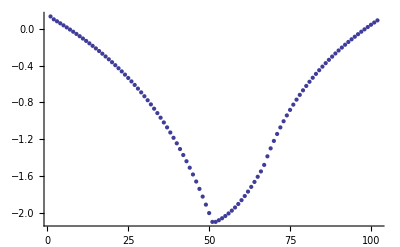

```mathematica
val=Table[ResultL[[i,1]],{i,Length[ResultL]}]
ListPlot[val]
ClearAll[val]
```

```mathematica
Length[ListETotalL]
Length[ResultIJL]
```

102

102

```mathematica
(*DeformElastL2=Table[ToIJ[ListETotalL2[[i]]-FromIJ[ResultIJL2[[i,2]]]],{i,1,Length[ResultL2]}];
SigElastIJL2=Table[{K DeformElastL2[[i,1]],2 G DeformElastL2[[i,2]],DeformElastL2[[i,3]]}/.exemple,{i,1,Length[ResultL2]}];
SigElastIJLplot=Table[{K DeformElastL2[[i,1]],2 G DeformElastL2[[i,2]]}/.exemple,{i,1,Length[ResultL2]}];
gl=ListPlot[SigElastIJLplot]
Show[gl,bg]
Diff=Table[SigElastIJL2[[i]]-ResultIJL2[[i,3]],{i,1,Length[ResultL2]}]//Chop
Table[Function1[ResultIJL2[[i,3,1]],ResultIJL2[[i,3,2]]],{i,1,Length[ResultL2]}]*)
```

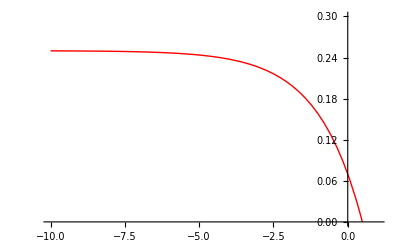

```mathematica
bg
```

```mathematica
ResultIJL[[2,4]]
ToIJ[ListETotalL[[2]]]
FromIJ[ResultIJL[[2,2]]]
ToIJ[ListETotalL[[2]]-FromIJ[ResultIJL[[2,2]]]]
```

{-0.26,15.0111,1}

{-0.0013,0.000750555,1}

{-0.00146543,-0.000170389}

{0.000506205,2.8646×10^-6,1}

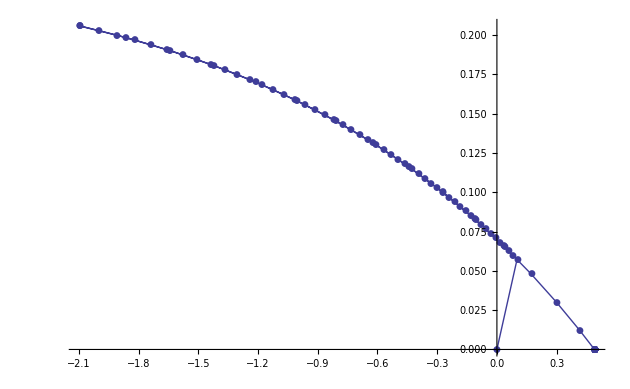

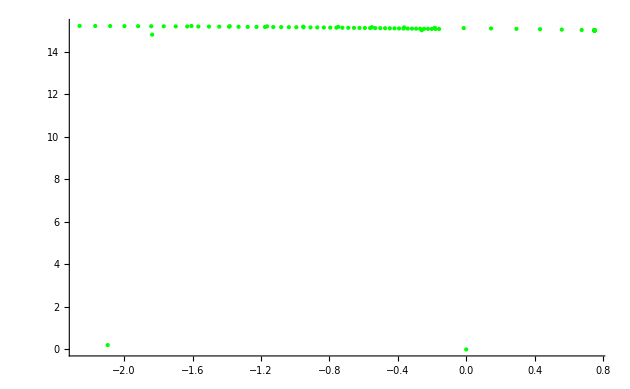

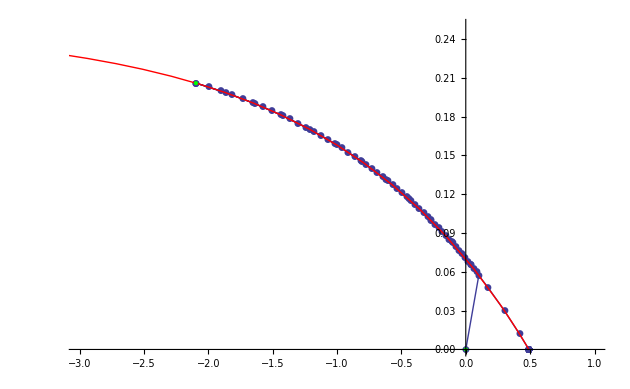

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,-2},{0,0,0},{0,0,0}}

{-0.07,-0.0000747017,-0.0000508588,-0.0000522874,-0.0000536916,-0.000055033,-0.0000563112,-0.0000575257,-0.000058676,-0.0000597615,-0.0000607815,-0.0000617354,-0.0000626221,-0.0000634406,-0.0000641895,-0.0000648674,-0.0000654724,-0.0000660024,-0.0000664551,-0.0000668277,-0.0000671172,-0.0000673202,-0.000067433,-0.0000674514,-0.0000673712,-0.0000671876,-0.0000668957,-0.0000664905,-0.0000659667,-0.0000653192,-0.0000645427,-0.0000636324,-0.0000625836,-0.0000613923,-0.000060055,-0.0000585694,-0.0000569341,-0.0000551491,-0.0000532164,-0.0000511396,-0.0000489246,-0.00004658,-0.000044117,-0.0000415498,-0.0000388959,-0.000036176,-0.0000334138,-0.0000306362,-0.0000278727,-0.0000251546,-0.0000225145,-0.0000225145,7.63278×10^-17,4.85723×10^-17,5.55112×10^-17,1.38778×10^-17,4.16334×10^-17,4.16334×10^-17,2.77556×10^-17,5.55112×10^-17,2.77556×10^-17,2.77556×10^-17,2.77556×10^-17,2.77556×10^-17,0.,-5.55112×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17}

```mathematica
DeformElastL=Table[ToIJ[ListETotalL[[i]]-FromIJ[ResultIJL[[i,2]]]],{i,1,Length[ListETotalL]}];
SigElastIJL=Table[{3K DeformElastL[[i,1]],2 G DeformElastL[[i,2]],DeformElastL[[i,3]]}/.exemple,{i,1,Length[ListETotalL]}];
SigElastIJL2=Table[{3K DeformElastL[[i,1]],2 G DeformElastL[[i,2]]}/.exemple,{i,1,Length[ListETotalL]}];
SigTrialIJL=Table[{ResultIJL[[i,4,1]],ResultIJL[[i,4,2]]},{i,Length[ResultIJL]}];
gl=ListPlot[SigElastIJL2,PlotJoined->True,PlotMarkers->Automatic]
gl2=ListPlot[SigTrialIJL,PlotStyle->{Green}]
Show[gl,bg,gl2,PlotRange->{{-3,1},{0,0.25}}]
Diff=Table[SigElastIJL[[i]]-ResultIJL[[i,3]],{i,1,Length[ListETotalL]}]//Chop
Table[Function1[ResultIJL[[i,3,1]],ResultIJL[[i,3,2]]],{i,1,Length[ListETotalL]}]
```

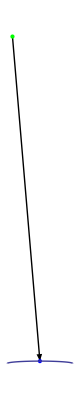

```mathematica
ShowPoint[i_]:=Block[{frompoint,topoint,arrow,dot1,dot2,ellips},
frompoint={ResultIJL[[i,4,1]],ResultIJL[[i,4,2]]};
topoint={ResultIJL[[i,3,1]],ResultIJL[[i,3,2]]};
arrow=Graphics[{Arrowheads[0.02],Arrow[{frompoint,topoint}]}];
dot1=Graphics[{PointSize[Large],Green,Point[frompoint]}];
dot2=Graphics[{PointSize[Large],Blue,Point[topoint]}];
ellips=Ag[ResultL[[i,1]]];
{arrow,dot1,dot2,ellips}
]
Show[ShowPoint[20]]
```

```mathematica
Animate[Show[ShowPoint[i],PlotRange->{{-3,2},{-0.1,0.4}}],{i,1,Length[ResultIJL],1},AnimationRunning->False]
```

```mathematica
Animate[Show[gl,bg,gl2,ShowPoint[i],PlotRange->{{-3,1},{0,0.25}}],{i,1,Length[ResultIJL],1},AnimationRunning->False]
```

```mathematica
TableShowPoint=Table[Show[gl,bg,gl2,ShowPoint[i],PlotRange->{{-3,1},{0,0.25}}],{i,1,Length[ResultIJL]}];
string=NotebookDirectory[];
FileAnimationL=string<>"AnimationL.gif";
Export[FileAnimationL,TableShowPoint]
```

/Users/phil/Dropbox/projeto_labmec_2011_14/Plasticidade/Aprendizado/AnimationL.gif

{{0.,0},{-0.0013,-0.0324082},{-0.0026,-0.0425707},{-0.0039,-0.0529565},{-0.0052,-0.0635142},{-0.0065,-0.074249},{-0.0078,-0.085167},{-0.0091,-0.0962742},{-0.0104,-0.107577},{-0.0117,-0.119082},{-0.013,-0.130796},{-0.0143,-0.142728},{-0.0156,-0.154883},{-0.0169,-0.167272},{-0.0182,-0.179901},{-0.0195,-0.192782},{-0.0208,-0.205922},{-0.0221,-0.219332},{-0.0234,-0.233023},{-0.0247,-0.247006},{-0.026,-0.261293},{-0.0273,-0.275896},{-0.0286,-0.290829},{-0.0299,-0.306106},{-0.0312,-0.321742},{-0.0325,-0.337753},{-0.0338,-0.354156},{-0.0351,-0.370968},{-0.0364,-0.388208},{-0.0377,-0.405898},{-0.039,-0.424058},{-0.0403,-0.442712},{-0.0416,-0.461884},{-0.0429,-0.4816},{-0.0442,-0.501889},{-0.0455,-0.52278},{-0.0468,-0.544305},{-0.0481,-0.566499},{-0.0494,-0.589398},{-0.0507,-0.613041},{-0.052,-0.63747},{-0.0533,-0.66273},{-0.0546,-0.688868},{-0.0559,-0.715936},{-0.0572,-0.743987},{-0.0585,-0.773081},{-0.0598,-0.803277},{-0.0611,-0.834643},{-0.0624,-0.867246},{-0.0637,-0.901158},{-0.065,-0.936457},{-0.065,-0.936457},{-0.0637,-0.393077},{-0.0624,-0.328089},{-0.0611,-0.266251},{-0.0598,-0.207857},{-0.0585,-0.153184},{-0.0572,-0.102472},{-0.0559,-0.0559139},{-0.0546,-0.0136387},{-0.0533,0.0242974},{-0.052,0.05792},{-0.0507,0.0873382},{-0.0494,0.11274},{-0.0481,0.134383},{-0.0468,0.152581},{-0.0455,0.163435},{-0.0442,0.163435},{-0.0429,0.163435},{-0.0416,0.163435},{-0.0403,0.163435},{-0.039,0.163435},{-0.0377,0.163435},{-0.0364,0.163435},{-0.0351,0.163435},{-0.0338,0.163435},{-0.0325,0.163435},{-0.0312,0.163435},{-0.0299,0.163435},{-0.0286,0.163435},{-0.0273,0.163435},{-0.026,0.163435},{-0.0247,0.163435},{-0.0234,0.163435},{-0.0221,0.163435},{-0.0208,0.163435},{-0.0195,0.163435},{-0.0182,0.163435},{-0.0169,0.163435},{-0.0156,0.163435},{-0.0143,0.163435},{-0.013,0.163435},{-0.0117,0.163435},{-0.0104,0.163435},{-0.0091,0.163435},{-0.0078,0.163435},{-0.0065,0.163435},{-0.0052,0.163435},{-0.0039,0.163435},{-0.0026,0.163435},{-0.0013,0.163435},{0.,0.163435}}

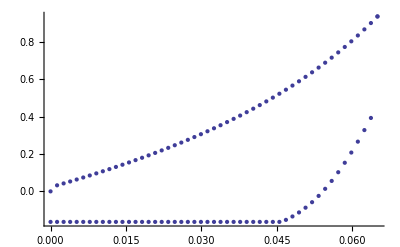

```mathematica
a=Table[{ListETotalL[[i,1]],ResultL[[i,3,1]]},{i,1,Length[ListETotalL]}]
ga=ListPlot[-a]
Clear[a,b,ga,gb]
```

```mathematica
a=Derivatives[Result[[1,3]],Result[[2,3]]-Result[[1,3]],Result[[1,1]]];
{{a[[1,1]]Sqrt[3],a[[1,2]]},{a[[2,1]]Sqrt[3],a[[2,2]]},a[[3]]}
{ListETotal[[2]],Result[[2,2]],Result[[2,1]]}
```

lval = 0.133045

flval = 0.0532179

gradf2 = {-26.0371,0.}

derivT = {-0.00191967,0.0157458}

dlval = 17.0081

B lval = 0.08914

- C B E^(B lval) = -0.131844

dfval = -2.24242

one = 255.675

two = 84.2732

three = 0.

four = 0.

df2depsp = 339.949

epspponto = -0.00014703

trN2 = -45.0976

gammaponto = 3.26026×10^-6

deformPlast = {-0.0000848878,0.}

ST = {0,1}

deformElast = {-0.0000166248,0.000196822}

{{-0.000175825,0.000196822},{-0.00014703,0.},-0.00014703}

{{-0.000325,0.000187639},{-0.000275126,0.0000484644},-0.000275126}

```mathematica
ElastoPlastic[Result[[1,1]],Result[[1,2]],ListETotal[[2]]]
```

ETotal = {-0.000325,0.000187639}

SigI1xJ2 = {-0.0216667,0.0150111}

valf2 = 0.431788

subit {I1T→-0.0216667,J2T→0.0150111}

θ = -π

θ = -(19 π)/20

θ = -(9 π)/10

θ = -(17 π)/20

θ = -(4 π)/5

θ = -(3 π)/4

θ = -(7 π)/10

θ = -(13 π)/20

θ = -(3 π)/5

θ = -(11 π)/20

θ = -π/2

θ = -(9 π)/20

θ = -(2 π)/5

θ = -(7 π)/20

θ = -(3 π)/10

θ = -π/4

θ = -π/5

θ = -(3 π)/20

θ = -π/10

θ = -π/20

θ = 0

θ = π/20

θ = π/10

θ = (3 π)/20

θ = π/5

θ = π/4

θ = (3 π)/10

θ = (7 π)/20

θ = (2 π)/5

θ = (9 π)/20

θ = π/2

θ = (11 π)/20

θ = (3 π)/5

θ = (13 π)/20

θ = (7 π)/10

θ = (3 π)/4

θ = (4 π)/5

θ = (17 π)/20

θ = (9 π)/10

θ = (19 π)/20

θ = π

restheta = {5.67729,5.34003,5.12872,4.9867,4.87787,4.78283,4.69152,4.5989,4.5027,4.4021,4.29704,4.18782,4.07487,3.9587,3.83975,3.71847,3.59526,3.47045,3.34437,3.21729,3.08947,2.96115,3.45065,3.57936,3.70797,3.83632,3.96425,4.09163,4.21839,4.34455,4.47028,4.59604,4.72284,4.85265,4.98938,5.14073,5.32211,5.56417,5.91817,0.122311,0.605891}

θ = (19 π)/20

θ = (19 π)/20

residue = {0.122311,0.00034957}

tangent = {{3.32067,-242.53},{-0.000312192,1.33818}}

delu = {0.0568818,0.000274499}

θ = 2.92763

delepsp = -0.000274499

θ = 2.92763

residue = {-0.0229419,3.22682×10^-6}

tangent = {{4.02657,-202.504},{-0.000428652,1.33871}}

delu = {-0.00566767,5.95617×10^-7}

θ = 2.9333

delepsp = -0.000275094

θ = 2.9333

residue = {0.0000914666,3.16371×10^-8}

tangent = {{4.05591,-225.014},{-0.000417475,1.33881}}

delu = {0.0000242825,3.12026×10^-8}

θ = 2.93327

delepsp = -0.000275126

θ = 2.93327

residue = {-1.41228×10^-9,5.93007×10^-13}

tangent = {{4.05592,-224.935},{-0.000417523,1.33881}}

delu = {-3.29334×10^-10,3.40229×10^-13}

θ = 2.93327

delepsp = -0.000275126

θ = 2.93327

residue = {0.,1.6263×10^-19}

tangent = {{4.05592,-224.935},{-0.000417523,1.33881}}

delu = {6.85528×10^-18,1.23612×10^-19}

θ = 2.93327

delepsp = -0.000275126

θ = 2.93327

residue = {0.,5.42101×10^-20}

Function2 = 2.22045×10^-16

{-0.000275126,{-0.000275126,0.0000484644},{-0.00332496,0.011134}}

```mathematica
{K,2G}/.exemple
{ListETotal[[2,1]]K,ListETotal[[2,2]]2G}/.exemple
(%-Result[[2,3]])/.exemple
{%[[1]]/K,%[[2]]/(2G)}/.exemple
```

{66.6667,80}

{-0.216667,0.150111}

{-0.179007,0.117562}

{-0.0026851,0.00146953}

```mathematica
Result[[2]]
```

{-0.000275126,{-0.000275126,0.0000484644},{-0.00332496,0.011134}}

```mathematica
epsp=Result[[2,1]]
theta=2.5604883056356527;
l=LFunction[epsp];
fl=F[l]/.exemple;
i1theta=l+fl R Cos[theta]/.exemple;
i1=Result[[2,3,1]];
i1-i1theta;
sqj2=Result[[2,3,2]];
sqj2theta=fl Sin[theta];
sqj2theta-sqj2;
(l-i1)^2 /(fl R)^2 + sqj2^2/fl^2 -1/.exemple;
gfv1=2√3(i1-l)/(fl R)^2/.exemple;
√3 gfv1;
gfv2=√2 sqj2/fl^2;
sqj2/fl;
ep=Result[[2,2]];
ArcTan[ep[[1]],ep[[2]]]
epprop={6(i1-l)/(fl R)^2,(2sqj2)/fl^2}/.exemple
ArcTan[epprop[[1]],epprop[[2]]]
TmTt={K epprop[[1]],2G epprop[[2]]}/.exemple
sigtrial={ListETotal[[2,1]]K,ListETotal[[2,2]]2G}/.exemple;
sigma=Result[[2,3]]
difsigma=(sigtrial-sigma)/.exemple;
ArcTan[difsigma[[1]],difsigma[[2]]]
ep-{difsigma[[1]]/K,difsigma[[2]]/(2G)}/.exemple
ArcTan[TmTt[[1]],TmTt[[2]]]
ArcTan[2 G R difsigma[[1]],3K difsigma[[2]]]/.exemple
theta
difsigma

Print[" delta gamma ",δγ2=epsp/epprop[[1]]]
Tepprop={K epprop[[1]],2G epprop[[2]]}/.exemple;
toto=Tepprop δγ2
ArcTan[difsigma[[1]],difsigma[[2]]]
ArcTan[toto[[1]],toto[[2]]]
δγ2 epprop-ep


Print["Checking stress functions"];
sigma
sqj2
l
fl
Print["gradf ",{epprop[[1]]/Sqrt[3],epprop[[2]]/Sqrt[2]}]
{sigma[[1]]/Sqrt[3],sigma[[2]]Sqrt[2]}

DLFunction[epsp]
B l/.exemple
dF[l]/.exemple
DLFunction[epsp]dF[l]/.exemple
a=DLFunction[epsp](2(l-i1))/(fl R)^2/.exemple
b=DLFunction[epsp](-(2(l-i1)^2)/(fl^3 R^2)dF[l])/.exemple
c=DLFunction[epsp](-(2sigma[[2]]^2)/fl^3 dF[l])/.exemple
Print["four ",DLFunction[epsp](-(2sigma[[2]]^2)/1 dF[l])/.exemple]
dfedep=DLFunction[epsp]((2(l-i1))/(fl R)^2-(2(l-i1)^2)/(fl^3 R^2)dF[l]-(2sqj2^2)/fl^3 dF[l])/.exemple
gradFT=epprop[[1]] sigma[[1]]/3+epprop[[2]] sigma[[2]]
(*Function2[sigma[[1]],sigma[[2]],epsp]-Function2[0,0,epsp]
Function2[sigma[[1]],sigma[[2]],0]-Function2[0,0,0]
*)
Print["epponto " ,a=epponto=-gradFT/dfedep]
Print["TrN2 ",epprop[[1]]]
Print["gammaponto ",gammaponto=epponto/epprop[[1]]]

epsp=0;
i1=0;
sqj2=0;
epprop={6(i1-l)/(fl R)^2,(2sqj2)/fl^2}/.exemple;
dfedep=DLFunction[epsp]((2(l-i1))/(fl R)^2-(2(l-i1)^2)/(fl^3 R^2)dF[l]-(2sqj2^2)/fl^3 dF[l])/.exemple
gradFT=epprop[[1]] sigma[[1]]/3+epprop[[2]] sigma[[2]]
(*Function2[sigma[[1]],sigma[[2]],epsp]-Function2[0,0,epsp]
Function2[sigma[[1]],sigma[[2]],0]-Function2[0,0,0]
*)
Print["epponto " ,b=epponto=-gradFT/dfedep]
Print["epponto medio ",(a+b)/2]
Print["TrN2 ",epprop[[1]]]
Print["gammaponto ",gammaponto=epponto/epprop[[1]]]


ClearAll[l,fl,i1,sqj2,gfv1,gfv2,epsp,theta,i1theta,sqj2theta,ep,epprop,TmTt,sigtrial,sigma,difsigma,Tepprop,toto,δγ2,dfedep,gradFT,epponto,a,b,c,gammaponto]
```

-0.000275126

2.96723

{-43.6165,7.68321}

2.96723

{-2907.77,614.657}

{-0.00332496,0.011134}

2.93327

{0.,0.}

2.93327

2.93327

2.56049

{-0.0183417,0.00387715}

delta gamma 6.30783×10^-6

{-0.0183417,0.00387715}

2.93327

2.93327

{5.42101×10^-20,-4.06576×10^-20}

Checking stress functions

{-0.00332496,0.011134}

0.011134

0.128354

0.0538354

gradf {-25.182,5.43285}

{-0.00191967,0.0157458}

17.0926

0.0859971

-0.13143

-2.24649

248.507

79.888

3.56967

four 0.000556972

331.965

0.133886

epponto -0.000403313

TrN2 -43.6165

gammaponto 9.2468×10^-6

316.564

0.0471204

epponto -0.00014885

epponto medio -0.000276081

TrN2 -42.5151

gammaponto 3.5011×10^-6

```mathematica
K
```

K